```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work"]
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC\Projects\VELA\Work

```mathematica
gunfiles=Join[
FileNames["*Gun_fine_crestingData*",{"\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018"},3],
FileNames["*Gun_fine_crestingData*",{"\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019"},3]
];
```

```mathematica
linacfiles=Join[
FileNames["*Linac1_fine_crestingData*",{"\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018"},3],
FileNames["*Linac1_fine_crestingData*",{"\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019"},3]
];
```

```mathematica
Clear[x,y,a,b]
```

```mathematica
getDate[file_]:=FileDate[file,"Creation"]
```

```mathematica
findPythonFit[datafile_]:=Check[Block[{xData,yData,a,b,crest,x,y,approxcrest,weights,fit,data},
{xData,yData}=Import[datafile,{"Data",{"/xData","/yData"}}];
xData=If[#≥0,#,#+360]&/@xData;
data=Transpose[{xData,yData}];
approxcrest=crest/.FindFit[data,eq=a+b(crest-x)^2,{a,b,crest},x];
weights=(1+(yData-Min[(yData)]))*(1+Abs[(xData-approxcrest)])^0.5;
fit=NonlinearModelFit[data,eq=a+b(crest-x)^2,{a,b,crest},x,Weights->1/weights]["BestFitParameters"];
{getDate[datafile],approxcrest,crest/.fit}
],Nothing]
```

```mathematica
gunfiles[[1]]
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC\Projects\VELA\Work\2018\06\14\174942_Gun_fine_crestingData.h5

```mathematica
gunCrest=Quiet[findPythonFit[#]]&/@gunfiles;
```

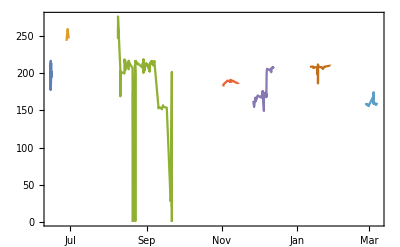

```mathematica
DateListPlot[Split[gunCrest[[All,{1,3}]],#2[[1]]-#1[[1]]<Quantity[1,"Week"]&]]
```

```mathematica
linacCrest=Quiet[findPythonFit[#]]&/@linacfiles;
```

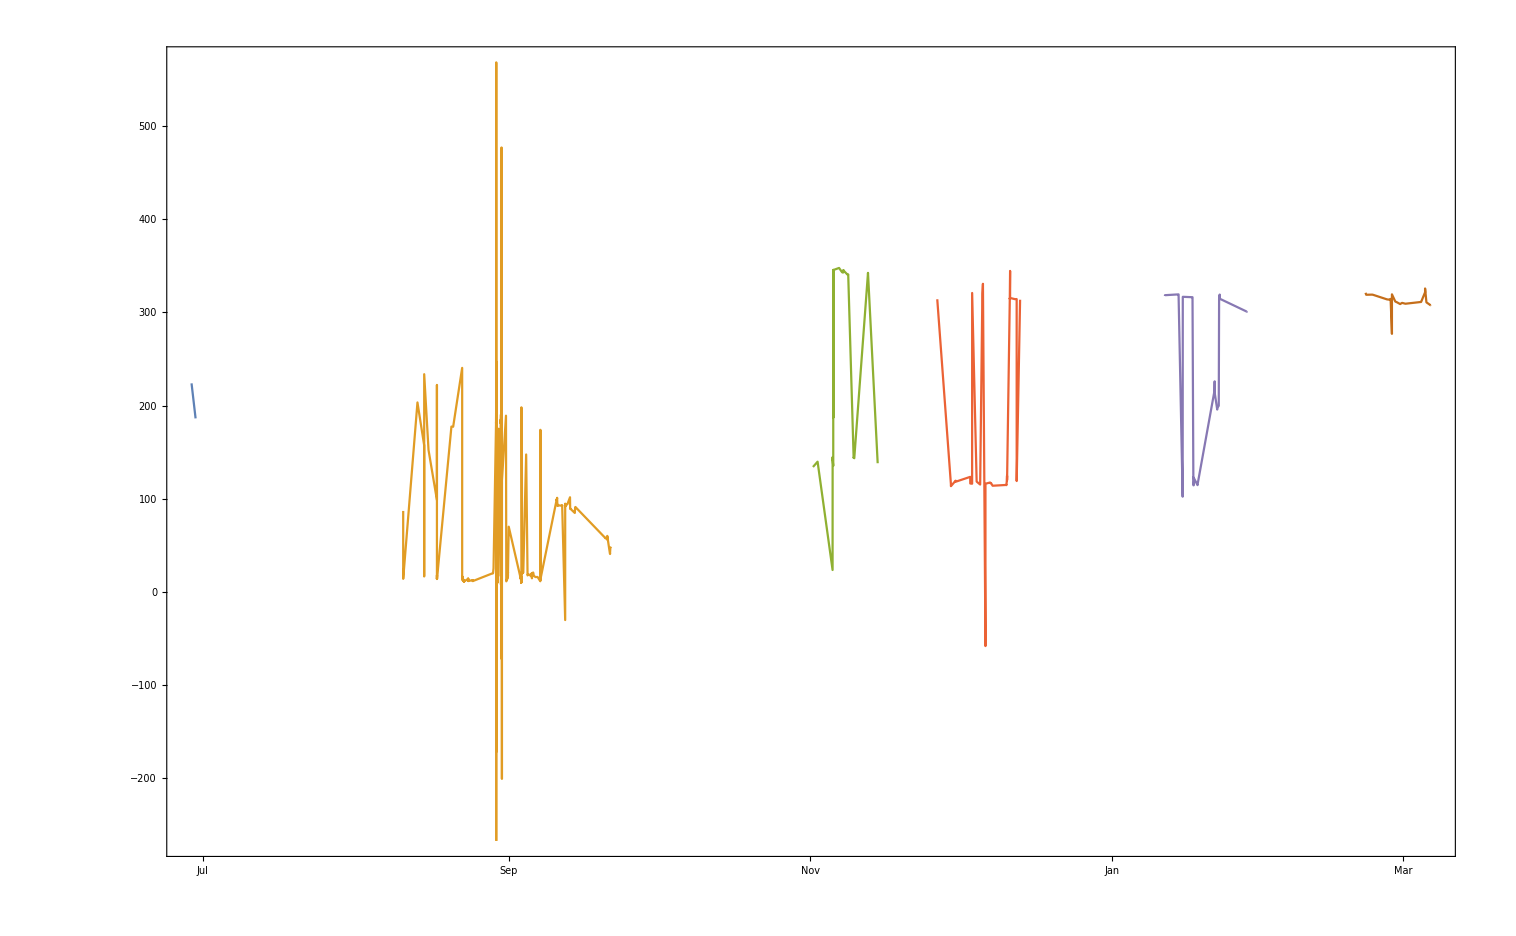

```mathematica
DateListPlot[Split[linacCrest[[All,{1,3}]],#2[[1]]-#1[[1]]<Quantity[1,"Week"]&]]
```